```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Crea redes aleatorias BernoulliGraphDistribution

```mathematica
(*results=Table[RandomGraph[BernoulliGraphDistribution[VertexCount[data[[i]]],probabilidades[[i]]]], {i ,7}];
```

#### Crea redes aleatorias WattsStrogatzGraphDistribution

```mathematica
(*resultsWatts=Table[GraphDistanceMatrix[RandomGraph[WattsStrogatzGraphDistribution[i,0.5]]], {i ,{1098,  7, 130, 45,110,12,22 }}];*)
(*resultsWatts=Table[RandomGraph[WattsStrogatzGraphDistribution[VertexCount[data[[i]]],probabilidades[[i]]]], {i ,7}];
```

#### Crea redes aleatorias BarabasiAlbertGraphDistribution

```mathematica
(*resultsBarabais=Table[RandomGraph[BarabasiAlbertGraphDistribution[i,3]], {i ,{1098,  7, 130, 45,110,12,22 }}];
```

#### Cargar redes de coautoria

```mathematica
red1=Import["s.NET"];
```

```mathematica
red1
```

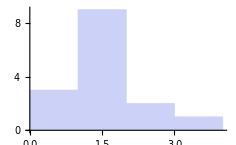

```mathematica
Histogram[VertexDegree[red1]]
```

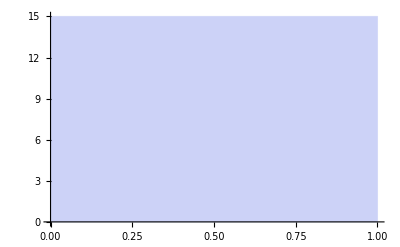

```mathematica
Histogram[LocalClusteringCoefficient[red1]]
```

```mathematica
HighlightGraph[red1,VertexSize->Thread[VertexList[red1]->%]]
```

```mathematica
red2 =Import["c.NET"]
```

-Graphics-

```mathematica
FindShortestPath[%35,All,All]
```

```mathematica
Histogram[ShortestPathFunction[{All,All},«»]]
```

Histogram::ldata: ShortestPathFunction[{All, All}, {1, « 2 », {{{0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, « 1 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 1 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, « 1 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 1 »}, « 44 », {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 1 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 1 »}, « 1 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 43 », {« 1 »}, {« 1 »}, {« 1 »}, « 1 »}}] is not a valid dataset or list of datasets.

Histogram[ShortestPathFunction[{All,All},{1,«2»,{{{0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},«45»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{«1»},{«1»},{{«1»},«50»},«44»,{«1»},{«1»},{«1»}}}]]

```mathematica
WeightedGraphQ[%16]
```

True

```mathematica
FindShortestPath[%16,All,All]
```

ShortestPathFunction[{All,All},«»]

```mathematica
CommunityGraphPlot[red2]
```

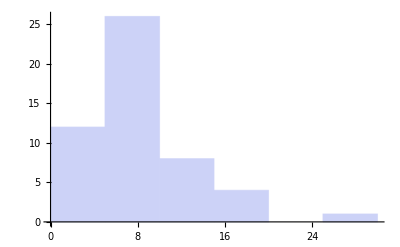

```mathematica
Histogram[VertexDegree[red2]]
```

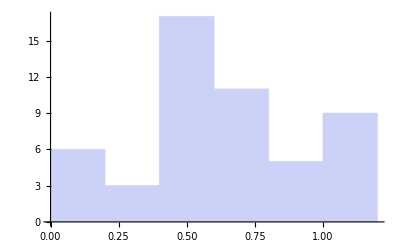

```mathematica
Histogram[LocalClusteringCoefficient[red2]]
```

```mathematica
Plot[VertexDegree[red2],LocalClusteringCoefficient[red2]]
VertexDegree[red2]
```

Plot::pllim: Range specification LocalClusteringCoefficient[red2] is not of the form {x, xmin, xmax}.

Plot[VertexDegree[red2],LocalClusteringCoefficient[red2]]

{9,15,8,9,7,1,2,1,28,12,12,15,7,13,5,18,7,5,2,2,19,11,5,7,6,5,7,4,11,9,8,11,2,5,6,8,3,4,12,6,5,5,8,2,7,4,5,5,8,10,2}

```mathematica
x = VertexDegree[red2]
y = LocalClusteringCoefficient[red2]
```

```mathematica
t =Table[{x[[i]],y[[i]]},{i,Length[x]}]
```

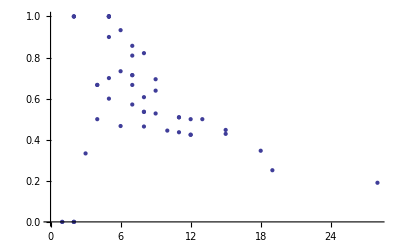

```mathematica
ListPlot[t]
```

```mathematica
red3 =Import["sc.NET"]
```

-Graphics-

-Graphics-

```mathematica
Histogram[VertexDegree[red3]]
```

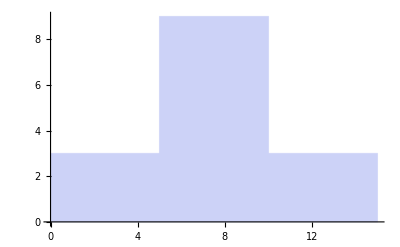

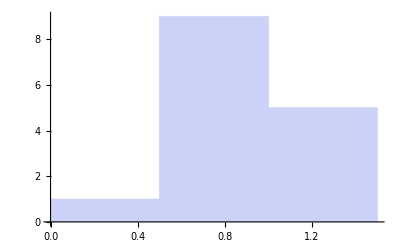

```mathematica
Histogram[LocalClusteringCoefficient[red3]]
```

```mathematica
CommunityGraphPlot[red3]
```

-Graphics-

{2,11,0,6,7,9,6,6,12,8,6,11,4,5,7}

{1,29/55,0,1,16/21,2/3,11/15,1,17/33,11/14,1,3/5,2/3,1,17/21}

{{2,1},{11,29/55},{0,0},{6,1},{7,16/21},{9,2/3},{6,11/15},{6,1},{12,17/33},{8,11/14},{6,1},{11,3/5},{4,2/3},{5,1},{7,17/21}}

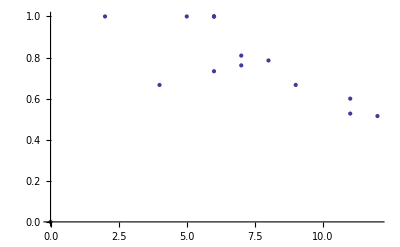

```mathematica
u = VertexDegree[red3]
p = LocalClusteringCoefficient[red3]
k =Table[{x[[i]],y[[i]]},{i,Length[x]}]
ListPlot[k]
```

```mathematica
red4 =Import["NetData/35-2001.NET"];
```

```mathematica
red5 =Import["NetData/35-2007.NET"];
```

```mathematica
red6 =Import["NetData/69-2001.NET"];
```

```mathematica
red7 =Import["NetData/69-2007.NET"];
```

```mathematica
data={red1, red2 ,red3 ,red4, red5, red6, red7};
```

```mathematica
VertexCount[data[[1]]]
```

1098

```mathematica
probabilidades=Table[EdgeCount[data[[i]]]/(VertexCount[data[[i]]]*(VertexCount[data[[i]]]-1)),{i,1,7,1}]
```

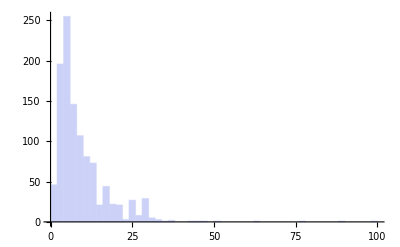
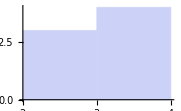
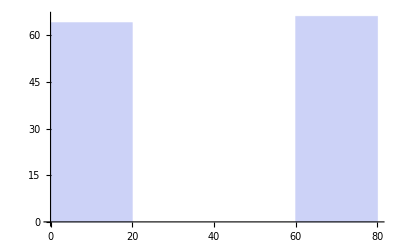
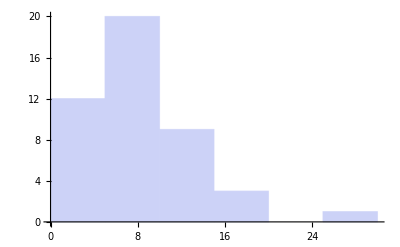
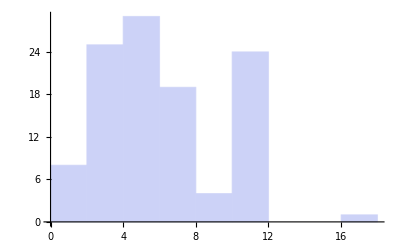
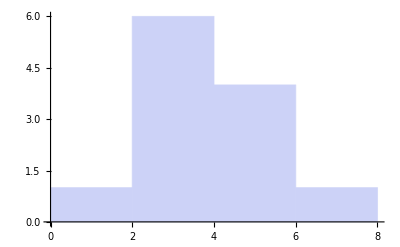
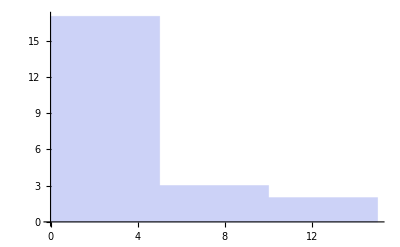

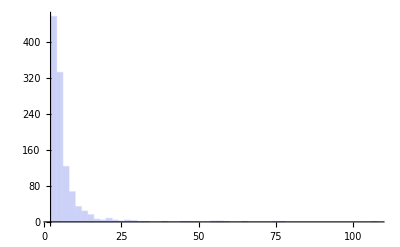

```mathematica
Table[Histogram[VertexDegree[data[[i]]]],{i,7}]
Table[Histogram[VertexDegree[resultsBarabais[[i]]]],{i,7}]
Table[Histogram[VertexDegree[resultsWatts[[i]]]],{i,7}]
Table[Histogram[VertexDegree[results[[i]]]],{i,7}]
```

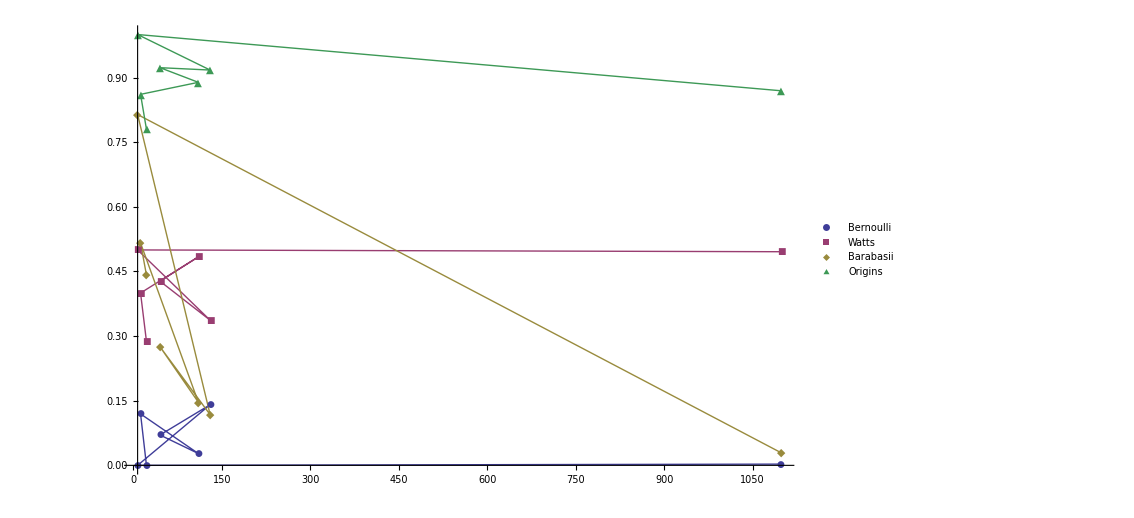

```mathematica
ListPlot[{Table[{VertexCount[results[[i]]],MeanClusteringCoefficient[results[[i]]]},{i,7}],Table[{VertexCount[resultsWatts[[i]]],MeanClusteringCoefficient[resultsWatts[[i]]]},{i,7}],Table[{VertexCount[resultsBarabais[[i]]],MeanClusteringCoefficient[resultsBarabais[[i]]]},{i,7}],Table[{VertexCount[data[[i]]],MeanClusteringCoefficient[data[[i]]]},{i,1,7}]}, DataRange->{0,2000}, PlotRange->All,PlotMarkers->Automatic,Joined-> True,PlotLegends->{"Bernoulli","Watts","Barabasii","Origins"}]
```

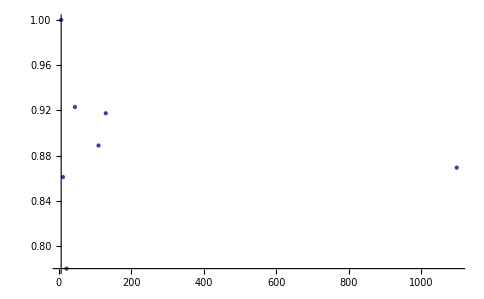

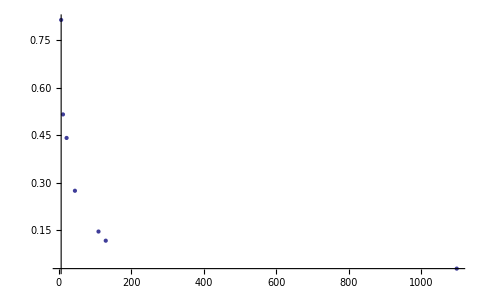

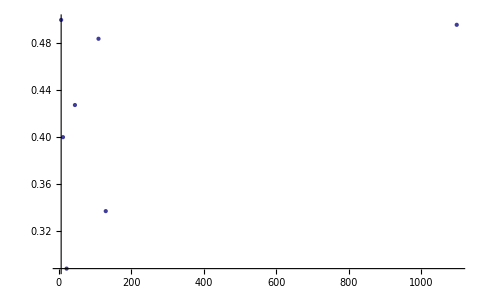

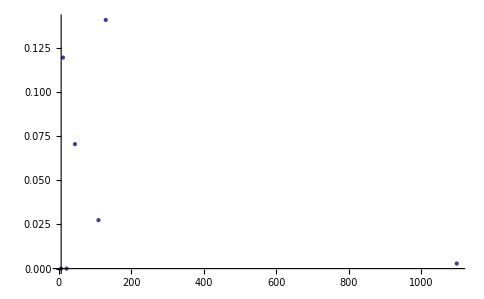

```mathematica
ListPlot[Table[{VertexCount[data[[i]]],MeanClusteringCoefficient[data[[i]]]},{i,1,7}], DataRange->{0,2000}, PlotRange->All,PlotMarkers->Automatic]
ListPlot[Table[{VertexCount[resultsBarabais[[i]]],MeanClusteringCoefficient[resultsBarabais[[i]]]},{i,7}],   PlotRange->All]
ListPlot[Table[{VertexCount[resultsWatts[[i]]],MeanClusteringCoefficient[resultsWatts[[i]]]},{i,7}], PlotRange->All]
ListPlot[Table[{VertexCount[results[[i]]],MeanClusteringCoefficient[results[[i]]]},{i,7}],PlotRange->All]
```

```mathematica
g=Graph[{"Moreno P."->"Cristancho M.","Vargas V.M."->"Diaz J.F.","Hochsztain E."->"Pena J.M.","Millan S."->"Pena J.M.","Perez J.A."->"Pabon G.","Tischer I."->"Gutierrez J.M.","Diaz N."->"Tischer I.","Bernal A."->"Moreno P.","Florian B."->"Munoz F.","Rodriguez-R L.M."->"Bernal A.","Rueda C."->"Assayag G.","Bacca-Cortes E.B."->"Munoz F.","Valencia F."->"Diaz J.F.","Florian B."->"Specht M.","Velez P.E."->"Naik A.K.","Vargas D."->"Chaves D.","Alvarez G."->"Assayag G.","Gonzalez-Aranda P."->"Menasalvas E.","Gonzalo-Martin C."->"Millan S.","Grajales A."->"Zambrano M.M.","Hermith D."->"Guzman M.","Millan S."->"Marban O.","Jordan R."->"Rueda C.","Pereira R.T."->"Millan M.","Pinzon A."->"Zambrano M.M.","Millan M."->"Trujillo M.","Aranda J."->"Versari C.","Valencia F.D."->"Versari C.","Specht M."->"Fabregat Gesa R.","Sierra R."->"Bernal A.","Restrepo S."->"Pinzon A.","Millan S."->"Perez M.S.","Amador S."->"Tischer I.","Diaz J.F."->"Ortiz V.J.","Quesada L.O."->"Tamura G.","Rodriguez-R L.M."->"Barreto E.","Millan M."->"Machuca F.","Jordan R."->"Diaz J.F.","Florian B."->"Solarte O.","Duarte J.E."->"Moreno P.A.","Pabon M.C."->"Montoya G.A.","Restrepo S."->"Gonzalez A.","Drachsler H."->"Fabregat Gesa R.","Moreno P.A."->"Tobar F.","Tamura G."->"Diaz J.F.","Gutierrez J.M."->"Tobar F.","Bedoya O."->"Tischer I.","Rueda C."->"Alvarez G.","Rueda C."->"Quesada L.O.","Glahn C."->"Fabregat Gesa R.","Alvarez G."->"Diaz J.F.","Chiarugi D."->"Falaschi M.","Moreno P."->"Gonzalez A.","Martinez E."->"Gutierrez J.M.","Pinzon A."->"Castro H.","Restrepo S."->"Zambrano M.M.","Guzman M."->"Olarte C.A.","Barreto E."->"Zambrano M.M.","Sierra R."->"Barreto E.","Caicedo N.G."->"Lozano C.A.","Zambrano M.M."->"Cristancho M.","Ruiz E.M."->"Baeza R.P.","Pinzon A."->"Gonzalez A.","Grajales A."->"Barreto E.","Bernal A."->"Zambrano M.M.","Florian B."->"Fabregat R.","Garreta L.E."->"Amador S.","Tobar-Tosse F."->"Moreno P.A.","Gutierrez J.M."->"Garcia F.","Timaran R."->"Millan M.","Chiarugi D."->"Hermith D.","Moreno P."->"Castro H.","Falaschi M."->"Hermith D.","Dorado A."->"Millan M.","Alvarez G."->"Quesada L.O.","Garreta L.E."->"Gutierrez J.M.","Amador S."->"Garcia F.","Glahn C."->"Specht M.","Ruiz C."->"Segovia J.","Delgado A."->"Jordan R.","Costumero R."->"Menasalvas E.","Fernandez-BaizaN M.C."->"Baeza R.P.","Di Giusto C."->"Nielsen M.","Tobar H.F."->"Moreno P.A.","Grajales A."->"Castro H.","Cristancho M."->"Gonzalez A.","Pabon G."->"Diaz J.F.","Garreta L.E."->"Martinez E.","Moreno P.A."->"Naik A.K.","Cabezas I."->"Padilla V.","Lozano C.A."->"Gutierrez G.","Pinzon A."->"Sierra R.","Cabezas I."->"Florian M.","Gutierrez G."->"Rueda C.","Mejia-Carmona D.F."->"Tischer I.","Aranda J."->"Valencia F.D.","Chamorro C.R."->"Pinedo C.R.","Velasco-Medina J."->"Moreno P.A.","Arcila O."->"Dinas S.","Martinez A.T."->"Banos A.G.","Rodriguez-R L.M."->"Moreno P.","Ceballos O."->"Garcia A.","Pena J.M."->"Marban O.","Diaz N."->"Gutierrez J.M.","Aranda J."->"Di Giusto C.","Nielsen M."->"Valencia F.D.","Baldiris S.M."->"Gesa R.F.","Santamaria M."->"Trujillo M.","Mossos N."->"Mejia-Carmona D.F.","Pinzon A."->"Rodriguez-R L.M.","Delgado A."->"Rueda C.","Restrepo S."->"Cristancho M.","Corradini F."->"Valencia F.D.","Perez J.A."->"Diaz J.F.","Menasalvas E."->"Ruiz C.","Cacciagrano D."->"Corradini F.","Pabon G."->"Jordan R.","Delgado A."->"Diaz J.F.","Millan M."->"Ortiz E.","Micheli G.C."->"Bueno J.A.","Trujillo M."->"Pineres J.","Menasalvas E."->"Perez M.S.","Cacciagrano D."->"Valencia F.D.","Velez P.E."->"Garcia F.","Vargas G."->"Millan M.","Trujillo M."->"Salazar L.","Pabon G."->"Rueda C.","Caicedo N.G."->"Gutierrez G.","Florian B."->"Glahn C.","Sierra R."->"Gonzalez A.","Chaves D."->"Pineres J.","Martinez E."->"Diaz N.","Millan M."->"Menasalvas E.","Diaz J.F."->"Mena J.A.","Tamura G."->"Assayag G.","Costumero R."->"Garcia-Pedrero A.","Alvarez G."->"Valencia F.","Aranda J."->"Diaz J.F.","Millan S."->"Gonzalez P.","Naik A.K."->"Tobar F.","Restrepo S."->"Barreto E.","Barreto E."->"Moreno P.","Menasalvas E."->"Hadjimichael M.","Gonzalez A."->"Castro H.","Garreta L.E."->"Diaz N.","Sierra R."->"Moreno P.","Caicedo N.G."->"Olarte C.A.","Garcia-Pedrero A."->"Gonzalo-Martin C.","Garcia-Castro L."->"Millan M.","Padilla V."->"Florian M.","Hochsztain E."->"Tasistro A.","Gaona C.M."->"Kuklinski W.S.","Bautista Rodolfo"->"Diaz J.F.","Amador S."->"Naik A.K.","Gonzalo-Martin C."->"Menasalvas E.","Giraldo C.A."->"Munoz F.","Bautista Rodolfo"->"Millan M.","Diaz J.F."->"Assayag G.","Gutierrez G."->"Olarte C.A.","Giusto C.D."->"Palamidessi C.","Garreta L.E."->"Garcia F.","Garreta L.E."->"Tischer I.","Martinez M."->"Dorado A.","Arcila O."->"Banon J.M.","Martinez E."->"Amador S.","Tobar H.F."->"Velez P.E.","Pinzon A."->"Barreto E.","Velez P.E."->"Martinez E.","Garreta L.E."->"Naik A.K.","Sierra R."->"Grajales A.","Florian B."->"De La Hoz Manotas A.","Menasalvas E."->"Segovia J.","Velez P.E."->"Gutierrez J.M.","Lozano C.A."->"Rueda C.","Rodriguez-R L.M."->"Sierra R.","Cacciagrano D."->"Aranda J.","Gonzalez-Aranda P."->"Segovia J.","Restrepo S."->"Grajales A.","Drachsler H."->"Specht M.","Amador S."->"Gutierrez J.M.","Hochsztain E."->"Pardo B.","Barreto E."->"Gonzalez A.","Quesada L.O."->"Valencia F.","Ceballos O."->"Millan M.","Montoya G.A."->"Millan M.","Calderon D.B."->"Trujillo M.","Aranda J."->"Ortiz V.J.","Lozano C.A."->"Diaz J.F.","Bernal A."->"Gonzalez A.","Palamidessi C."->"Valencia F.D.","Olarte C.A."->"Rueda C.","Barreto E."->"Cristancho M.","Garcia A."->"Millan M.","Zambrano M.M."->"Castro H.","Velez P.E."->"Tobar F.","Rueda C."->"Tamura G.","Pardo B."->"Menasalvas E.","Diaz J.F."->"Rueda C.","Delgado C.A."->"Guerrero F.G.","Gutierrez J.M."->"Naik A.K.","Restrepo S."->"Rodriguez-R L.M.","Rodriguez-R L.M."->"Grajales A.","Rueda C."->"Valencia F.","Aranda J."->"Palamidessi C.","Chavarriaga O."->"Florian B.","Velez P.E."->"Garreta L.E.","Villegas L.E.M."->"Carrillo P.J.R.","Martinez E."->"Tobar F.","Giraldo C.A."->"Bacca-Cortes E.B.","Tamura G."->"Valencia F.","Chavarriaga O."->"Solarte O.","Baldiris S.M."->"De La Hoz Manotas A.","Aranda J."->"Perez J.A.","Pinzon A."->"Grajales A.","Menasalvas E."->"Tasistro A.","Grajales A."->"Gonzalez A.","Padilla V."->"Trujillo M.","Fernandez-BaizaN M.C."->"Ruiz E.M.","Roncancio C."->"Millan M.","Cabezas I."->"Trujillo M.","Caicedo N.G."->"Diaz J.F.","Martinez E."->"Naik A.K.","Aranda J."->"Giusto C.D.","Menasalvas E."->"Gonzalez P.","Bernal A."->"Castro H.","Chaves D."->"Trujillo M.","Vargas D."->"Pineres J.","Diaz J.F."->"Guerrero F.G.","Diaz N."->"Tobar F.","Micheli G.C."->"Diaz J.F.","Grajales A."->"Cristancho M.","Martinez E."->"Moreno P.A.","Lopez F."->"Gonzalo-Martin C.","Restrepo S."->"Sierra R.","Hadjimichael M."->"Marban O.","Delgado A."->"Perez J.A.","Diaz J.F."->"Arboleda H.","Gutierrez J.M."->"Moreno P.A.","Bernal A."->"Cristancho M.","Tobar-Tosse F."->"Velez P.E.","Lopez F."->"Millan M.","Chaves D."->"Barraza J.","Tobar-Tosse F."->"Rodriguez A.C.","Perez M.S."->"Tasistro A.","Gonzalez-Aranda P."->"Ruiz C.","Diaz N."->"Moreno P.A.","Valencia F."->"Assayag G.","Rodriguez A.C."->"Velez P.E.","Millan M."->"Baeza R.P.","Millan S."->"Menasalvas E.","Millan M."->"Fernandez-BaizaN M.C.","Quesada L.O."->"Assayag G.","Pardo B."->"Pena J.M.","Trujillo M."->"Ortiz E.","Pena J.M."->"Hadjimichael M.","Tobar-Tosse F."->"Zambrano M.M.","Pinzon A."->"Cristancho M.","Diaz N."->"Amador S.","Glahn C."->"Drachsler H.","Trujillo M."->"Barraza J.","Hermith D."->"Olarte C.A.","Garreta L.E."->"Tobar F.","Martinez M."->"Millan M.","Pineres J."->"Barraza J.","Perez M.S."->"Hochsztain E.","Garcia D."->"Millan M.","Vargas G."->"Dorado A.","Quesada L.O."->"Diaz J.F.","Diaz J.F."->"Gutierrez G.","Delgado A."->"Pabon G.","Amador S."->"Tobar F.","Mera C."->"Trujillo M.","Aranda J."->"Rueda C.","Tischer I."->"Tobar F.","Sierra R."->"Castro H.","Garcia-Pedrero A."->"Millan S.","Zambrano M.M."->"Gonzalez A.","Lozano C.A."->"Olarte C.A.","Dinas S."->"Banon J.M.","Vargas V.M."->"Arboleda H.","Rodriguez A.C."->"Moreno P.A.","Baldiris S.M."->"Fabregat R.","Giraldo C.A."->"Florian B.","Martinez M."->"Vargas G.","Pereira R.T."->"Machuca F.","Rodriguez-R L.M."->"Castro H.","Millan M."->"Ruiz E.M.","Rodriguez-R L.M."->"Cristancho M.","Barreto E."->"Castro H.","Velez P.E."->"Moreno P.A.","Tischer I."->"Naik A.K.","Rodriguez-R L.M."->"Zambrano M.M.","Millan S."->"Pardo B.","Trujillo M."->"Florian M.","Hochsztain E."->"Millan S.","Caicedo N.G."->"Rueda C.","Costumero R."->"Lopez F.","Florian B."->"Gomez F.","Millan S."->"Ruiz C.","Tobar F."->"Garcia F.","Velez P.E."->"Amador S.","Millan S."->"Hadjimichael M.","Costumero R."->"Millan S.","Gomez F."->"Munoz F.","Martinez E."->"Tischer I.","Diaz N."->"Garcia F.","Florian B."->"Drachsler H.","Zambrano M.M."->"Moreno P.A.","Chiarugi D."->"Olarte C.A.","Florian B."->"Gesa R.F.","Diaz J.F."->"Bueno J.A.","Grajales A."->"Moreno P.","Sierra R."->"Cristancho M.","Pabon M.C."->"Millan M.","Martinez E."->"Garcia F.","Moreno P.A."->"Garcia F.","Guevara-Mendez D."->"Bedoya O.","Duarte J.E."->"Velasco-Medina J.","Gonzalez-Aranda P."->"Millan S.","Amador S."->"Moreno P.A.","Menasalvas E."->"Marban O.","Alvarez G."->"Tamura G.","Fabregat R."->"De La Hoz Manotas A.","Cristancho M."->"Castro H.","Rueda C."->"Valencia F.D.","Aranda J."->"Nielsen M.","Sierra R."->"Zambrano M.M.","Tischer I."->"Moreno P.A.","Tischer I."->"Garcia F.","Moreno P."->"Zambrano M.M.","Pinzon A."->"Moreno P.","Velez P.E."->"Zambrano M.M.","Florian B."->"Baldiris S.M.","Millan M."->"Diaz J.F.","Ceballos O."->"Garcia-Castro L.","Bacca-Cortes E.B."->"Gomez F.","De Pinerez Reyes R.E.G."->"Diaz J.F.","Millan S."->"Tasistro A.","Naik A.K."->"Garcia F.","Garcia A."->"Garcia-Castro L.","Chiarugi D."->"Guzman M.","Falaschi M."->"Olarte C.A.","Florian B."->"Fabregat Gesa R.","Diaz N."->"Naik A.K.","Restrepo S."->"Castro H.","Restrepo S."->"Bernal A.","Rueda C."->"Olarte C.A.","Corradini F."->"Aranda J.","Velez P.E."->"Tischer I.","Costumero R."->"Millan M.","Giusto C.D."->"Valencia F.D.","Restrepo S."->"Moreno P.","Bernal A."->"Barreto E.","Gonzalo-Martin C."->"Millan M.","Mossos N."->"Tischer I.","Diaz J.F."->"Olarte C.A.","Garreta L.E."->"Moreno P.A.","Rodriguez A.C."->"Zambrano M.M.","Grajales A."->"Bernal A.","Di Giusto C."->"Valencia F.D.","Costumero R."->"Gonzalo-Martin C.","Pena J.M."->"Menasalvas E.","Pinzon A."->"Bernal A.","Garcia-Pedrero A."->"Menasalvas E.","Delgado C.A."->"Diaz J.F.","Giraldo C.A."->"Gomez F.","Florian B."->"Bacca-Cortes E.B.","Mazo C."->"Salazar L.","Perez J.A."->"Jordan R.","Pabon M.C."->"Roncancio C.","Perez J.A."->"Valencia F.D.","Vargas D."->"Trujillo M.","Millan S."->"Segovia J.","Vargas D."->"Barraza J.","Rodriguez-R L.M."->"Gonzalez A.","Falaschi M."->"Guzman M.","Mazo C."->"Trujillo M.","Hochsztain E."->"Menasalvas E.","Lopez F."->"Menasalvas E.","Perez J.A."->"Rueda C.","Velez P.E."->"Diaz N.","Duarte D. D.D."->"Gaona C.M."},DirectedEdges->False]
```

Graph::supp: Mixed graphs and multigraphs are not supported.

Graph[{Moreno P.→Cristancho M.,Vargas V.M.→Diaz J.F.,Hochsztain E.→Pena J.M.,Millan S.→Pena J.M.,Perez J.A.→Pabon G.,Tischer I.→Gutierrez J.M.,Diaz N.→Tischer I.,Bernal A.→Moreno P.,Florian B.→Munoz F.,Rodriguez-R L.M.→Bernal A.,Rueda C.→Assayag G.,Bacca-Cortes E.B.→Munoz F.,Valencia F.→Diaz J.F.,Florian B.→Specht M.,Velez P.E.→Naik A.K.,Vargas D.→Chaves D.,Alvarez G.→Assayag G.,Gonzalez-Aranda P.→Menasalvas E.,Gonzalo-Martin C.→Millan S.,Grajales A.→Zambrano M.M.,Hermith D.→Guzman M.,Millan S.→Marban O.,Jordan R.→Rueda C.,Pereira R.T.→Millan M.,Pinzon A.→Zambrano M.M.,Millan M.→Trujillo M.,Aranda J.→Versari C.,Valencia F.D.→Versari C.,Specht M.→Fabregat Gesa R.,Sierra R.→Bernal A.,Restrepo S.→Pinzon A.,Millan S.→Perez M.S.,Amador S.→Tischer I.,Diaz J.F.→Ortiz V.J.,Quesada L.O.→Tamura G.,Rodriguez-R L.M.→Barreto E.,Millan M.→Machuca F.,Jordan R.→Diaz J.F.,Florian B.→Solarte O.,Duarte J.E.→Moreno P.A.,Pabon M.C.→Montoya G.A.,Restrepo S.→Gonzalez A.,Drachsler H.→Fabregat Gesa R.,Moreno P.A.→Tobar F.,Tamura G.→Diaz J.F.,Gutierrez J.M.→Tobar F.,Bedoya O.→Tischer I.,Rueda C.→Alvarez G.,Rueda C.→Quesada L.O.,Glahn C.→Fabregat Gesa R.,Alvarez G.→Diaz J.F.,Chiarugi D.→Falaschi M.,Moreno P.→Gonzalez A.,Martinez E.→Gutierrez J.M.,Pinzon A.→Castro H.,Restrepo S.→Zambrano M.M.,Guzman M.→Olarte C.A.,Barreto E.→Zambrano M.M.,Sierra R.→Barreto E.,Caicedo N.G.→Lozano C.A.,Zambrano M.M.→Cristancho M.,Ruiz E.M.→Baeza R.P.,Pinzon A.→Gonzalez A.,Grajales A.→Barreto E.,Bernal A.→Zambrano M.M.,Florian B.→Fabregat R.,Garreta L.E.→Amador S.,Tobar-Tosse F.→Moreno P.A.,Gutierrez J.M.→Garcia F.,Timaran R.→Millan M.,Chiarugi D.→Hermith D.,Moreno P.→Castro H.,Falaschi M.→Hermith D.,Dorado A.→Millan M.,Alvarez G.→Quesada L.O.,Garreta L.E.→Gutierrez J.M.,Amador S.→Garcia F.,Glahn C.→Specht M.,Ruiz C.→Segovia J.,Delgado A.→Jordan R.,Costumero R.→Menasalvas E.,Fernandez-BaizaN M.C.→Baeza R.P.,Di Giusto C.→Nielsen M.,Tobar H.F.→Moreno P.A.,Grajales A.→Castro H.,Cristancho M.→Gonzalez A.,Pabon G.→Diaz J.F.,Garreta L.E.→Martinez E.,Moreno P.A.→Naik A.K.,Cabezas I.→Padilla V.,Lozano C.A.→Gutierrez G.,Pinzon A.→Sierra R.,Cabezas I.→Florian M.,Gutierrez G.→Rueda C.,Mejia-Carmona D.F.→Tischer I.,Aranda J.→Valencia F.D.,Chamorro C.R.→Pinedo C.R.,Velasco-Medina J.→Moreno P.A.,Arcila O.→Dinas S.,Martinez A.T.→Banos A.G.,Rodriguez-R L.M.→Moreno P.,Ceballos O.→Garcia A.,Pena J.M.→Marban O.,Diaz N.→Gutierrez J.M.,Aranda J.→Di Giusto C.,Nielsen M.→Valencia F.D.,Baldiris S.M.→Gesa R.F.,Santamaria M.→Trujillo M.,Mossos N.→Mejia-Carmona D.F.,Pinzon A.→Rodriguez-R L.M.,Delgado A.→Rueda C.,Restrepo S.→Cristancho M.,Corradini F.→Valencia F.D.,Perez J.A.→Diaz J.F.,Menasalvas E.→Ruiz C.,Cacciagrano D.→Corradini F.,Pabon G.→Jordan R.,Delgado A.→Diaz J.F.,Millan M.→Ortiz E.,Micheli G.C.→Bueno J.A.,Trujillo M.→Pineres J.,Menasalvas E.→Perez M.S.,Cacciagrano D.→Valencia F.D.,Velez P.E.→Garcia F.,Vargas G.→Millan M.,Trujillo M.→Salazar L.,Pabon G.→Rueda C.,Caicedo N.G.→Gutierrez G.,Florian B.→Glahn C.,Sierra R.→Gonzalez A.,Chaves D.→Pineres J.,Martinez E.→Diaz N.,Millan M.→Menasalvas E.,Diaz J.F.→Mena J.A.,Tamura G.→Assayag G.,Costumero R.→Garcia-Pedrero A.,Alvarez G.→Valencia F.,Aranda J.→Diaz J.F.,Millan S.→Gonzalez P.,Naik A.K.→Tobar F.,Restrepo S.→Barreto E.,Barreto E.→Moreno P.,Menasalvas E.→Hadjimichael M.,Gonzalez A.→Castro H.,Garreta L.E.→Diaz N.,Sierra R.→Moreno P.,Caicedo N.G.→Olarte C.A.,Garcia-Pedrero A.→Gonzalo-Martin C.,Garcia-Castro L.→Millan M.,Padilla V.→Florian M.,Hochsztain E.→Tasistro A.,Gaona C.M.→Kuklinski W.S.,Bautista Rodolfo→Diaz J.F.,Amador S.→Naik A.K.,Gonzalo-Martin C.→Menasalvas E.,Giraldo C.A.→Munoz F.,Bautista Rodolfo→Millan M.,Diaz J.F.→Assayag G.,Gutierrez G.→Olarte C.A.,Giusto C.D.→Palamidessi C.,Garreta L.E.→Garcia F.,Garreta L.E.→Tischer I.,Martinez M.→Dorado A.,Arcila O.→Banon J.M.,Martinez E.→Amador S.,Tobar H.F.→Velez P.E.,Pinzon A.→Barreto E.,Velez P.E.→Martinez E.,Garreta L.E.→Naik A.K.,Sierra R.→Grajales A.,Florian B.→De La Hoz Manotas A.,Menasalvas E.→Segovia J.,Velez P.E.→Gutierrez J.M.,Lozano C.A.→Rueda C.,Rodriguez-R L.M.→Sierra R.,Cacciagrano D.→Aranda J.,Gonzalez-Aranda P.→Segovia J.,Restrepo S.→Grajales A.,Drachsler H.→Specht M.,Amador S.→Gutierrez J.M.,Hochsztain E.→Pardo B.,Barreto E.→Gonzalez A.,Quesada L.O.→Valencia F.,Ceballos O.→Millan M.,Montoya G.A.→Millan M.,Calderon D.B.→Trujillo M.,Aranda J.→Ortiz V.J.,Lozano C.A.→Diaz J.F.,Bernal A.→Gonzalez A.,Palamidessi C.→Valencia F.D.,Olarte C.A.→Rueda C.,Barreto E.→Cristancho M.,Garcia A.→Millan M.,Zambrano M.M.→Castro H.,Velez P.E.→Tobar F.,Rueda C.→Tamura G.,Pardo B.→Menasalvas E.,Diaz J.F.→Rueda C.,Delgado C.A.→Guerrero F.G.,Gutierrez J.M.→Naik A.K.,Restrepo S.→Rodriguez-R L.M.,Rodriguez-R L.M.→Grajales A.,Rueda C.→Valencia F.,Aranda J.→Palamidessi C.,Chavarriaga O.→Florian B.,Velez P.E.→Garreta L.E.,Villegas L.E.M.→Carrillo P.J.R.,Martinez E.→Tobar F.,Giraldo C.A.→Bacca-Cortes E.B.,Tamura G.→Valencia F.,Chavarriaga O.→Solarte O.,Baldiris S.M.→De La Hoz Manotas A.,Aranda J.→Perez J.A.,Pinzon A.→Grajales A.,Menasalvas E.→Tasistro A.,Grajales A.→Gonzalez A.,Padilla V.→Trujillo M.,Fernandez-BaizaN M.C.→Ruiz E.M.,Roncancio C.→Millan M.,Cabezas I.→Trujillo M.,Caicedo N.G.→Diaz J.F.,Martinez E.→Naik A.K.,Aranda J.→Giusto C.D.,Menasalvas E.→Gonzalez P.,Bernal A.→Castro H.,Chaves D.→Trujillo M.,Vargas D.→Pineres J.,Diaz J.F.→Guerrero F.G.,Diaz N.→Tobar F.,Micheli G.C.→Diaz J.F.,Grajales A.→Cristancho M.,Martinez E.→Moreno P.A.,Lopez F.→Gonzalo-Martin C.,Restrepo S.→Sierra R.,Hadjimichael M.→Marban O.,Delgado A.→Perez J.A.,Diaz J.F.→Arboleda H.,Gutierrez J.M.→Moreno P.A.,Bernal A.→Cristancho M.,Tobar-Tosse F.→Velez P.E.,Lopez F.→Millan M.,Chaves D.→Barraza J.,Tobar-Tosse F.→Rodriguez A.C.,Perez M.S.→Tasistro A.,Gonzalez-Aranda P.→Ruiz C.,Diaz N.→Moreno P.A.,Valencia F.→Assayag G.,Rodriguez A.C.→Velez P.E.,Millan M.→Baeza R.P.,Millan S.→Menasalvas E.,Millan M.→Fernandez-BaizaN M.C.,Quesada L.O.→Assayag G.,Pardo B.→Pena J.M.,Trujillo M.→Ortiz E.,Pena J.M.→Hadjimichael M.,Tobar-Tosse F.→Zambrano M.M.,Pinzon A.→Cristancho M.,Diaz N.→Amador S.,Glahn C.→Drachsler H.,Trujillo M.→Barraza J.,Hermith D.→Olarte C.A.,Garreta L.E.→Tobar F.,Martinez M.→Millan M.,Pineres J.→Barraza J.,Perez M.S.→Hochsztain E.,Garcia D.→Millan M.,Vargas G.→Dorado A.,Quesada L.O.→Diaz J.F.,Diaz J.F.→Gutierrez G.,Delgado A.→Pabon G.,Amador S.→Tobar F.,Mera C.→Trujillo M.,Aranda J.→Rueda C.,Tischer I.→Tobar F.,Sierra R.→Castro H.,Garcia-Pedrero A.→Millan S.,Zambrano M.M.→Gonzalez A.,Lozano C.A.→Olarte C.A.,Dinas S.→Banon J.M.,Vargas V.M.→Arboleda H.,Rodriguez A.C.→Moreno P.A.,Baldiris S.M.→Fabregat R.,Giraldo C.A.→Florian B.,Martinez M.→Vargas G.,Pereira R.T.→Machuca F.,Rodriguez-R L.M.→Castro H.,Millan M.→Ruiz E.M.,Rodriguez-R L.M.→Cristancho M.,Barreto E.→Castro H.,Velez P.E.→Moreno P.A.,Tischer I.→Naik A.K.,Rodriguez-R L.M.→Zambrano M.M.,Millan S.→Pardo B.,Trujillo M.→Florian M.,Hochsztain E.→Millan S.,Caicedo N.G.→Rueda C.,Costumero R.→Lopez F.,Florian B.→Gomez F.,Millan S.→Ruiz C.,Tobar F.→Garcia F.,Velez P.E.→Amador S.,Millan S.→Hadjimichael M.,Costumero R.→Millan S.,Gomez F.→Munoz F.,Martinez E.→Tischer I.,Diaz N.→Garcia F.,Florian B.→Drachsler H.,Zambrano M.M.→Moreno P.A.,Chiarugi D.→Olarte C.A.,Florian B.→Gesa R.F.,Diaz J.F.→Bueno J.A.,Grajales A.→Moreno P.,Sierra R.→Cristancho M.,Pabon M.C.→Millan M.,Martinez E.→Garcia F.,Moreno P.A.→Garcia F.,Guevara-Mendez D.→Bedoya O.,Duarte J.E.→Velasco-Medina J.,Gonzalez-Aranda P.→Millan S.,Amador S.→Moreno P.A.,Menasalvas E.→Marban O.,Alvarez G.→Tamura G.,Fabregat R.→De La Hoz Manotas A.,Cristancho M.→Castro H.,Rueda C.→Valencia F.D.,Aranda J.→Nielsen M.,Sierra R.→Zambrano M.M.,Tischer I.→Moreno P.A.,Tischer I.→Garcia F.,Moreno P.→Zambrano M.M.,Pinzon A.→Moreno P.,Velez P.E.→Zambrano M.M.,Florian B.→Baldiris S.M.,Millan M.→Diaz J.F.,Ceballos O.→Garcia-Castro L.,Bacca-Cortes E.B.→Gomez F.,De Pinerez Reyes R.E.G.→Diaz J.F.,Millan S.→Tasistro A.,Naik A.K.→Garcia F.,Garcia A.→Garcia-Castro L.,Chiarugi D.→Guzman M.,Falaschi M.→Olarte C.A.,Florian B.→Fabregat Gesa R.,Diaz N.→Naik A.K.,Restrepo S.→Castro H.,Restrepo S.→Bernal A.,Rueda C.→Olarte C.A.,Corradini F.→Aranda J.,Velez P.E.→Tischer I.,Costumero R.→Millan M.,Giusto C.D.→Valencia F.D.,Restrepo S.→Moreno P.,Bernal A.→Barreto E.,Gonzalo-Martin C.→Millan M.,Mossos N.→Tischer I.,Diaz J.F.→Olarte C.A.,Garreta L.E.→Moreno P.A.,Rodriguez A.C.→Zambrano M.M.,Grajales A.→Bernal A.,Di Giusto C.→Valencia F.D.,Costumero R.→Gonzalo-Martin C.,Pena J.M.→Menasalvas E.,Pinzon A.→Bernal A.,Garcia-Pedrero A.→Menasalvas E.,Delgado C.A.→Diaz J.F.,Giraldo C.A.→Gomez F.,Florian B.→Bacca-Cortes E.B.,Mazo C.→Salazar L.,Perez J.A.→Jordan R.,Pabon M.C.→Roncancio C.,Perez J.A.→Valencia F.D.,Vargas D.→Trujillo M.,Millan S.→Segovia J.,Vargas D.→Barraza J.,Rodriguez-R L.M.→Gonzalez A.,Falaschi M.→Guzman M.,Mazo C.→Trujillo M.,Hochsztain E.→Menasalvas E.,Lopez F.→Menasalvas E.,Perez J.A.→Rueda C.,Velez P.E.→Diaz N.,Duarte D. D.D.→Gaona C.M.},DirectedEdges→False]

```mathematica
Graph
```

gr

```mathematica
Import["autores3.net"]
```

-Graphics-

```mathematica
EdgeList[%3]
```

{1<->37,1<->38,1<->205,1<->341,1<->449,1<->593,1<->649,2<->329,3<->570,3<->709,4<->185,4<->198,4<->258,4<->286,4<->363,4<->571,4<->645,4<->650,4<->706,5<->116,5<->163,5<->364,5<->371,5<->390,5<->498,5<->582,6<->51,6<->66,6<->125,6<->226,6<->229,6<->238,6<->265,6<->288,6<->317,6<->346,6<->366,6<->412,6<->437,6<->497,6<->499,7<->132,7<->401,7<->507,7<->563,7<->641,7<->656,8<->33,8<->201,9<->481,9<->597,10<->255,10<->312,11<->53,11<->112,11<->220,11<->232,11<->384,11<->508,11<->549,12<->279,13<->344,14<->456,14<->614,15<->138,15<->381,15<->595,17<->150,17<->348,17<->464,18<->155,18<->329,19<->157,19<->197,19<->709,20<->491,20<->554,21<->49,21<->293,21<->324,21<->360,21<->385,21<->429,21<->561,21<->633,21<->645,21<->685,21<->721,22<->35,22<->39,23<->312,23<->359,24<->93,24<->564,25<->183,25<->362,25<->426,26<->741,26<->742,27<->118,27<->422,27<->462,27<->528,27<->533,28<->438,29<->418,30<->187,30<->315,30<->516,31<->143,31<->484,31<->676,32<->65,32<->78,33<->201,34<->154,34<->289,34<->326,34<->443,34<->469,34<->692,35<->39,36<->71,36<->83,36<->109,36<->237,36<->328,36<->369,36<->517,36<->566,36<->569,36<->694,36<->746,37<->38,37<->205,37<->341,37<->449,37<->593,37<->649,38<->205,38<->341,38<->449,38<->593,38<->649,40<->121,40<->495,40<->526,40<->744,41<->217,42<->312,42<->676,43<->69,43<->425,43<->518,43<->738,44<->57,44<->68,44<->86,44<->122,44<->147,44<->152,44<->274,44<->301,44<->322,44<->328,44<->534,44<->536,44<->548,44<->620,44<->628,45<->63,45<->73,45<->142,45<->329,45<->373,45<->389,45<->520,46<->676,47<->651,47<->655,48<->111,48<->135,48<->254,48<->375,48<->526,49<->293,49<->324,49<->360,49<->385,49<->429,49<->561,49<->633,49<->645,49<->685,49<->721,50<->126,51<->66,51<->265,51<->288,51<->317,51<->366,52<->257,52<->337,53<->220,54<->321,54<->531,54<->730,55<->207,55<->573,55<->599,56<->379,56<->435,56<->521,56<->592,56<->613,57<->68,57<->122,57<->147,57<->152,57<->322,57<->328,57<->534,57<->548,57<->628,58<->263,58<->382,58<->568,59<->446,60<->626,60<->666,61<->325,61<->380,61<->688,62<->85,62<->142,62<->373,63<->73,63<->329,63<->389,63<->520,64<->100,64<->115,64<->194,64<->290,64<->334,64<->455,64<->546,64<->661,64<->718,65<->78,66<->125,66<->226,66<->229,66<->238,66<->265,66<->288,66<->312,66<->317,66<->346,66<->366,66<->412,66<->437,66<->497,66<->499,66<->657,67<->222,67<->264,67<->733,68<->122,68<->147,68<->152,68<->322,68<->328,68<->534,68<->548,68<->628,69<->425,69<->518,69<->738,70<->302,70<->400,70<->459,70<->463,70<->466,71<->83,71<->109,71<->214,71<->237,71<->322,71<->328,71<->369,71<->517,71<->566,71<->569,71<->679,71<->694,71<->746,72<->376,72<->468,73<->329,73<->389,73<->520,74<->430,74<->450,74<->592,75<->89,75<->181,76<->170,76<->388,76<->434,76<->562,76<->592,76<->624,76<->629,77<->202,77<->275,77<->420,77<->708,79<->234,79<->415,79<->458,80<->132,80<->656,81<->113,81<->428,81<->629,81<->653,81<->696,82<->233,82<->530,82<->541,83<->109,83<->237,83<->328,83<->369,83<->517,83<->566,83<->569,83<->694,83<->746,84<->219,84<->368,85<->142,85<->373,86<->609,86<->620,87<->246,87<->592,88<->251,88<->349,88<->658,88<->669,89<->181,90<->142,90<->149,90<->373,91<->266,92<->682,92<->684,93<->564,94<->735,95<->130,95<->261,95<->282,96<->512,96<->527,96<->616,97<->167,97<->549,98<->137,98<->395,99<->485,99<->503,99<->542,100<->115,100<->194,100<->290,100<->334,100<->455,100<->546,100<->661,100<->718,101<->196,101<->210,101<->307,101<->637,102<->146,102<->253,103<->332,103<->442,104<->127,104<->287,104<->386,104<->598,104<->664,105<->472,105<->482,105<->723,105<->732,106<->460,107<->297,107<->298,108<->506,108<->511,108<->719,109<->237,109<->328,109<->369,109<->517,109<->566,109<->569,109<->694,109<->746,110<->454,111<->135,111<->254,111<->375,111<->526,112<->508,112<->549,113<->428,113<->629,113<->653,113<->696,114<->514,115<->194,115<->290,115<->334,115<->455,115<->546,115<->661,115<->718,116<->390,116<->498,116<->582,117<->260,117<->355,117<->680,118<->242,118<->250,118<->308,118<->422,118<->462,118<->528,118<->533,118<->602,118<->684,119<->219,119<->371,120<->554,120<->590,121<->495,121<->526,121<->744,122<->147,122<->152,122<->322,122<->328,122<->534,122<->548,122<->628,123<->190,123<->441,123<->607,124<->310,124<->408,124<->699,125<->238,125<->497,127<->287,127<->386,127<->598,127<->664,128<->239,128<->611,128<->707,128<->743,129<->216,129<->329,130<->261,130<->282,131<->247,131<->299,131<->350,132<->195,132<->208,132<->268,132<->311,132<->401,132<->507,132<->535,132<->563,132<->641,132<->656,133<->660,134<->319,134<->596,135<->156,135<->254,135<->281,135<->375,135<->457,135<->489,135<->526,135<->537,135<->583,135<->739,136<->154,136<->178,136<->223,136<->326,136<->443,136<->447,136<->453,136<->494,136<->519,136<->677,136<->692,136<->750,137<->343,137<->356,137<->395,137<->555,138<->381,138<->595,139<->344,139<->608,140<->146,140<->253,140<->262,140<->295,140<->515,140<->627,141<->520,141<->700,141<->704,142<->149,142<->372,142<->373,142<->448,142<->520,142<->604,142<->634,142<->687,143<->484,143<->648,143<->676,143<->728,144<->732,145<->260,145<->630,145<->644,145<->719,146<->182,146<->204,146<->209,146<->253,146<->262,146<->295,146<->405,146<->486,146<->505,146<->515,146<->627,146<->675,147<->152,147<->322,147<->328,147<->534,147<->548,147<->628,148<->166,148<->316,148<->323,148<->374,148<->698,148<->714,149<->373,150<->348,151<->383,152<->322,152<->328,152<->534,152<->548,152<->628,153<->445,153<->710,153<->720,154<->178,154<->199,154<->223,154<->289,154<->326,154<->443,154<->447,154<->453,154<->465,154<->469,154<->519,154<->538,154<->632,154<->677,154<->692,155<->329,156<->281,156<->457,156<->583,156<->739,157<->197,157<->709,158<->219,158<->559,158<->656,158<->683,159<->320,159<->331,160<->291,160<->433,160<->678,160<->745,161<->184,161<->329,161<->373,161<->382,161<->520,161<->705,162<->271,162<->304,162<->667,163<->364,163<->371,163<->582,164<->335,164<->473,165<->584,165<->659,166<->316,166<->323,166<->374,166<->698,166<->714,167<->549,167<->703,168<->224,169<->228,169<->532,170<->388,170<->434,170<->562,170<->592,170<->624,170<->629,171<->408,171<->699,172<->218,172<->318,173<->213,173<->241,173<->387,173<->646,174<->187,174<->592,174<->629,174<->697,175<->328,175<->655,176<->193,176<->452,176<->496,177<->256,177<->292,178<->223,178<->326,178<->443,178<->447,178<->453,178<->494,178<->519,178<->677,178<->692,178<->750,179<->408,179<->699,180<->309,180<->554,182<->204,182<->209,182<->405,182<->486,182<->505,182<->675,183<->362,183<->426,184<->329,184<->373,184<->382,184<->520,184<->705,185<->198,185<->258,185<->286,185<->363,185<->571,185<->645,185<->650,185<->706,186<->382,186<->568,186<->695,186<->736,187<->315,187<->516,187<->592,187<->629,187<->697,188<->621,188<->734,189<->432,190<->441,190<->607,191<->339,191<->347,191<->488,192<->324,192<->360,192<->385,192<->601,192<->645,192<->721,193<->452,193<->496,194<->290,194<->334,194<->455,194<->546,194<->661,194<->718,195<->208,195<->311,195<->656,196<->210,196<->307,196<->637,197<->709,198<->258,198<->286,198<->363,198<->571,198<->645,198<->650,198<->706,199<->326,199<->465,199<->538,199<->632,199<->677,199<->692,200<->617,200<->647,200<->662,202<->275,202<->420,202<->708,203<->329,203<->671,204<->209,204<->405,204<->486,204<->505,204<->675,205<->341,205<->449,205<->593,205<->649,206<->219,206<->348,206<->444,207<->573,207<->599,208<->264,208<->311,208<->656,208<->733,209<->405,209<->486,209<->505,209<->675,210<->307,210<->637,211<->342,211<->387,211<->477,211<->674,212<->230,212<->295,212<->467,212<->603,212<->610,212<->670,212<->729,213<->241,213<->587,213<->646,214<->322,214<->328,214<->679,215<->231,215<->235,215<->249,215<->338,215<->404,216<->329,216<->409,219<->348,219<->368,219<->371,219<->439,219<->444,219<->464,219<->559,219<->656,219<->683,221<->244,221<->345,221<->586,221<->672,222<->264,222<->733,223<->326,223<->443,223<->447,223<->453,223<->494,223<->519,223<->677,223<->692,223<->750,225<->329,225<->543,225<->560,227<->579,228<->236,228<->440,228<->532,228<->550,228<->565,229<->346,229<->437,230<->262,230<->295,230<->421,230<->467,230<->474,230<->603,230<->610,230<->627,230<->670,230<->729,231<->235,231<->249,231<->338,231<->404,232<->384,233<->530,233<->541,234<->415,234<->458,235<->249,235<->338,235<->404,236<->440,236<->550,236<->565,237<->328,237<->369,237<->517,237<->566,237<->569,237<->694,237<->746,238<->497,239<->611,239<->707,239<->743,240<->264,240<->325,241<->646,242<->308,242<->602,243<->270,243<->378,243<->509,243<->557,243<->631,244<->342,244<->345,244<->352,244<->361,244<->377,244<->476,244<->477,244<->580,244<->586,244<->672,245<->642,245<->690,246<->592,247<->299,247<->350,248<->354,248<->592,249<->338,249<->404,250<->684,251<->349,251<->658,251<->669,252<->294,252<->403,252<->556,252<->700,253<->262,253<->295,253<->515,253<->627,254<->375,254<->526,255<->312,255<->529,256<->292,257<->337,258<->286,258<->363,258<->571,258<->645,258<->650,258<->706,259<->732,260<->355,260<->630,260<->636,260<->644,260<->680,260<->719,260<->724,261<->282,262<->295,262<->421,262<->515,262<->627,263<->382,263<->568,264<->325,264<->733,265<->288,267<->611,268<->656,269<->348,269<->492,269<->572,269<->716,269<->726,270<->509,270<->510,270<->631,271<->300,271<->304,271<->667,272<->336,272<->340,272<->490,272<->719,273<->414,273<->680,274<->301,275<->420,275<->708,276<->391,276<->513,277<->284,277<->575,277<->622,278<->313,278<->419,278<->577,278<->681,280<->312,281<->457,281<->739,283<->545,284<->575,284<->622,285<->676,286<->363,286<->571,286<->645,286<->650,286<->706,287<->386,287<->598,287<->664,289<->326,289<->443,289<->469,289<->692,290<->334,290<->455,290<->546,290<->661,290<->718,291<->433,291<->678,291<->745,293<->324,293<->360,293<->385,293<->561,293<->633,293<->685,293<->721,294<->403,294<->556,294<->700,295<->421,295<->467,295<->515,295<->547,295<->553,295<->603,295<->610,295<->612,295<->627,295<->670,295<->729,296<->351,296<->717,297<->298,299<->350,302<->400,302<->459,302<->463,302<->466,303<->305,303<->397,303<->475,304<->667,305<->397,305<->475,306<->367,306<->407,306<->470,306<->504,307<->637,308<->602,309<->554,310<->408,310<->643,310<->699,311<->656,312<->346,312<->359,312<->365,312<->392,312<->410,312<->413,312<->437,312<->478,312<->529,312<->605,312<->657,312<->676,312<->715,312<->737,312<->740,312<->749,313<->419,313<->577,313<->681,314<->424,314<->471,314<->493,314<->673,315<->516,316<->323,316<->374,316<->698,316<->714,317<->366,317<->412,317<->499,319<->596,321<->531,321<->730,322<->328,322<->534,322<->548,322<->628,322<->679,323<->374,323<->698,323<->714,324<->360,324<->385,324<->429,324<->561,324<->601,324<->633,324<->645,324<->685,324<->721,325<->380,325<->427,325<->663,325<->688,326<->443,326<->447,326<->453,326<->465,326<->469,326<->494,326<->519,326<->538,326<->632,326<->677,326<->692,326<->750,327<->394,327<->524,327<->544,328<->369,328<->517,328<->534,328<->548,328<->566,328<->569,328<->628,328<->655,328<->679,328<->694,328<->746,329<->373,329<->382,329<->383,329<->389,329<->520,329<->543,329<->623,329<->671,329<->700,329<->705,329<->725,330<->357,332<->442,333<->665,333<->722,334<->455,334<->546,334<->661,334<->718,335<->473,336<->340,336<->490,336<->719,338<->404,339<->347,339<->488,340<->490,340<->719,341<->449,341<->593,341<->649,342<->387,342<->477,342<->674,343<->356,343<->395,343<->555,344<->608,345<->586,345<->672,346<->437,346<->657,347<->488,348<->439,348<->444,348<->464,348<->492,348<->572,348<->716,348<->726,349<->658,349<->669,351<->717,352<->361,352<->476,353<->581,353<->690,354<->592,354<->711,355<->680,356<->395,356<->555,358<->551,360<->385,360<->429,360<->561,360<->601,360<->633,360<->645,360<->685,360<->721,362<->426,363<->571,363<->645,363<->650,363<->706,364<->371,364<->582,365<->478,365<->749,367<->407,367<->470,367<->504,369<->517,369<->566,369<->569,369<->694,369<->746,370<->451,371<->582,372<->448,373<->382,373<->520,373<->604,373<->634,373<->687,373<->705,374<->698,374<->714,375<->526,376<->468,377<->580,378<->509,379<->521,379<->592,380<->688,381<->595,382<->520,382<->568,382<->695,382<->705,382<->736,383<->520,383<->623,383<->700,383<->725,385<->429,385<->561,385<->601,385<->633,385<->645,385<->685,385<->721,386<->598,386<->664,387<->477,387<->587,387<->646,387<->674,388<->434,388<->562,388<->592,388<->624,388<->629,389<->520,390<->498,390<->582,391<->513,392<->410,392<->715,393<->408,393<->699,394<->524,394<->544,395<->555,396<->436,396<->638,397<->475,398<->540,398<->701,399<->680,400<->459,400<->463,400<->466,401<->507,401<->563,401<->641,401<->656,402<->549,402<->607,403<->556,403<->700,405<->486,405<->505,405<->675,406<->479,406<->501,406<->727,407<->470,407<->504,408<->480,408<->502,408<->635,408<->686,408<->699,410<->715,411<->588,411<->691,412<->499,413<->737,413<->740,414<->680,415<->458,416<->427,416<->482,417<->539,417<->656,419<->577,419<->681,420<->708,421<->627,422<->462,422<->528,422<->533,424<->471,424<->493,424<->673,425<->518,425<->738,427<->482,427<->663,428<->629,428<->653,428<->696,429<->645,429<->685,430<->450,430<->592,431<->461,431<->500,431<->654,433<->678,433<->745,434<->562,434<->592,434<->624,434<->629,435<->521,435<->592,435<->613,436<->638,437<->657,439<->464,440<->550,440<->565,441<->607,442<->554,443<->447,443<->453,443<->469,443<->494,443<->519,443<->677,443<->692,443<->750,445<->710,445<->720,447<->453,447<->519,447<->677,447<->692,449<->593,449<->649,450<->592,452<->496,453<->494,453<->519,453<->677,453<->692,453<->750,455<->546,455<->661,455<->718,456<->614,457<->489,457<->537,457<->583,457<->739,459<->463,459<->466,461<->500,461<->654,462<->528,462<->533,463<->466,465<->538,465<->632,465<->677,465<->692,467<->603,467<->610,467<->670,467<->729,469<->692,470<->504,471<->493,471<->673,472<->482,472<->723,472<->732,474<->627,477<->674,478<->749,479<->501,479<->727,481<->567,481<->597,482<->723,482<->732,483<->652,484<->676,485<->503,485<->542,486<->505,486<->675,487<->611,487<->621,487<->640,489<->583,490<->719,491<->554,492<->572,492<->716,492<->726,493<->673,494<->519,494<->677,494<->692,494<->750,495<->526,495<->744,498<->582,500<->654,501<->727,502<->699,503<->542,505<->675,506<->511,506<->719,507<->563,507<->641,507<->656,508<->549,509<->557,509<->631,510<->578,510<->668,511<->719,512<->527,512<->616,515<->627,517<->566,517<->569,517<->694,517<->746,518<->738,519<->677,519<->692,519<->750,520<->623,520<->700,520<->704,520<->705,520<->725,521<->592,521<->613,522<->588,522<->676,523<->525,523<->594,524<->544,526<->744,527<->616,528<->533,530<->541,531<->730,534<->548,534<->628,535<->656,536<->552,537<->739,538<->632,538<->677,538<->692,539<->656,540<->701,545<->747,546<->661,546<->718,547<->553,547<->612,548<->628,549<->607,549<->703,549<->712,550<->565,553<->612,554<->590,556<->700,559<->656,559<->683,561<->633,561<->685,561<->721,562<->592,562<->624,562<->629,563<->641,563<->656,566<->569,566<->694,566<->746,567<->597,568<->695,568<->736,569<->694,569<->746,570<->709,571<->645,571<->650,571<->706,572<->716,572<->726,573<->599,574<->676,575<->622,576<->585,576<->600,576<->702,577<->681,578<->668,581<->690,584<->659,585<->702,586<->672,587<->646,588<->676,588<->691,591<->713,592<->613,592<->624,592<->629,592<->697,592<->711,593<->649,598<->664,601<->645,601<->721,603<->610,603<->670,603<->729,606<->611,607<->712,609<->620,610<->670,610<->729,611<->621,611<->640,611<->676,611<->707,611<->743,615<->693,617<->647,617<->662,618<->731,621<->640,621<->734,623<->700,623<->725,624<->629,625<->655,626<->666,629<->653,629<->696,629<->697,630<->644,632<->677,632<->692,633<->685,633<->721,634<->687,635<->699,636<->724,639<->748,641<->656,642<->690,644<->719,645<->650,645<->685,645<->706,645<->721,647<->662,648<->676,650<->706,651<->655,653<->696,656<->683,658<->669,661<->718,665<->722,670<->729,676<->728,676<->743,677<->692,677<->750,678<->745,682<->684,685<->721,686<->699,692<->750,694<->746,695<->736,698<->714,700<->704,700<->725,707<->743,710<->720,716<->726,723<->732,737<->740,741<->742}